```mathematica
WolframAlpha["integrate x/(cos(x)^2)",{{"IndefiniteIntegral",2},"Content"},PodStates->{"IndefiniteIntegral__Step-by-step solution"}]
```

Take the integral:
∫x sec^2(x)ⅆx
For the integrand x sec^2(x), integrate by parts, ∫fⅆg==f g-∫gⅆf, where 
 f==x,    ⅆg==sec^2(x) ⅆx,
ⅆf== ⅆx,     g==tan(x):
 == x tan(x)-∫tan(x)ⅆx
Rewrite tan(x) as (sin(x))/(cos(x)):
 == x tan(x)-∫(sin(x))/(cos(x))ⅆx
For the integrand (sin(x))/(cos(x)), substitute u==cos(x) and ⅆu==-sin(x) ⅆx:
 == x tan(x)-∫-1/uⅆu
Factor out constants:
 == x tan(x)+∫1/u ⅆu
The integral of 1/u is log(u):
 == log(u)+x tan(x)+constant
Substitute back for u==cos(x):
Answer: | 
 |  == x tan(x)+log(cos(x))+constant

```mathematica
Integrate[1/Cos[x]^2,x]
```

Tan[x]

```mathematica
Integrate[1/x^3,x]
```

-1/(2 x^2)

```mathematica
Integrate[Cos[Log[x]],x]
```

1/2 x Cos[Log[x]]+1/2 x Sin[Log[x]]

```mathematica
Integrate[x/(√(1+x)),x]
```

2/3 (-2+x) √(1+x)

```mathematica
∫_a^b x/(√(1+x))ⅆx===2∫_(√(1+a))^(√(1+b)) (u^2-1)ⅆu
```

False

```mathematica
Integrate[x/Cosh[x],x]
```

-ⅈ (x (Log[1-ⅈ ⅇ^-x]-Log[1+ⅈ ⅇ^-x])+PolyLog[2,-ⅈ ⅇ^-x]-PolyLog[2,ⅈ ⅇ^-x])

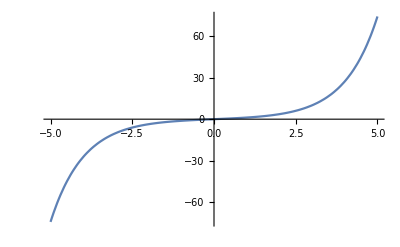

```mathematica
Plot[Sinh[x],{x, -5, 5}]
```

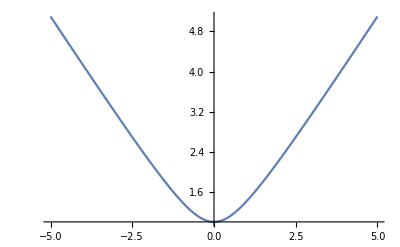

```mathematica
Plot[Cosh[ArcSinh[x]],{x, -5, 5}]
```

```mathematica
DSolve[y''[x]+y'[x]==x^4-8 x^3+7 x^2-5 x,y[x],x]
```

{{y[x]→91 x-(91 x^2)/2+(43 x^3)/3-3 x^4+x^5/5-ⅇ^-x C[1]+C[2]}}

```mathematica
Flatten[{{y[x]->91 x-(91 x^2)/2+(43 x^3)/3-3 x^4+x^5/5-ⅇ^-x C[1]+C[2]}}]
```

{y[x]→91 x-(91 x^2)/2+(43 x^3)/3-3 x^4+x^5/5-ⅇ^-x C[1]+C[2]}

```mathematica
DSolve[y''[x]+4y[x]==3x+3,y[x],x]
```

{{y[x]→(3 (1+x))/4+C[1] Cos[2 x]+C[2] Sin[2 x]}}

```mathematica
DSolve[y''[x]+3y'[x]+2y[x]==ⅇ^-x,y[x],x]
```

{{y[x]→ⅇ^-x (-1+x)+ⅇ^(-2 x) C[1]+ⅇ^-x C[2]}}

```mathematica
WolframAlpha["DSolve[y''[x]+3y'[x]+2y[x]==e^(-x),y[x],x]",{{"IndefiniteIntegral",2},"Content"},PodStates->{"IndefiniteIntegral__Step-by-step solution"}]
```

Missing[NotAvailable]

```mathematica
WolframAlpha["y''[x]+3y'[x]+2y[x]==e^(-x)",IncludePods->{"Differential equation solution"},PodStates->{"Step-by-step solution","Show all steps"}]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["y''[x]+y'[x]-2y[x]==8*sin(2x)",IncludePods->{"Differential equation solution"},PodStates->{"Step-by-step solution","Show all steps"}]
```

WolframAlphaQueryResults

```mathematica
DSolve[x*y'[x]+(x-1)*y[x]==x^2,y[x],x]
```

{{y[x]→x+ⅇ^-x x C[1]}}